```mathematica
P=-(ⅇ^(2 t Subscript[ω, 2]) k (k-2 m) Sin[(k (k-2 m) t)/(2 Subscript[r, 0]^2)])/Subscript[r, 0]^2+4 ⅇ^(4 t Subscript[ω, 2]) Subscript[ω, 2]+4 ⅇ^(2 t Subscript[ω, 2]) Cos[(k (k-2 m) t)/(2 Subscript[r, 0]^2)] Subscript[ω, 2];
```

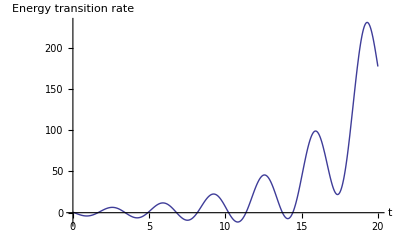

```mathematica
Plot[P/.{k->79,m->74,Subscript[r, 0]->37.9,Subscript[ω, 2]->0.08},{t,0,20},AxesLabel->{t,"Energy transition rate"}]
```

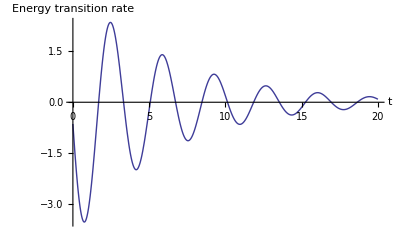

```mathematica
Plot[P/.{k->61.2,m->74,Subscript[r, 0]->37.9,Subscript[ω, 2]->-0.08},{t,0,20},AxesLabel->{t,"Energy transition rate"}]
```